```mathematica
ClearAll["Global*`"]
Clear["St","eps","b","A"]
$Assumptions = St > 0 && eps > 0 && b > 0 && b∈Reals && vS>0 && vS ∈Reals;
rules = {X ->( X0[#]+eps X1[#]+eps^2 X2[#]&),
z -> (z0[#]+eps z1[#]+ eps^2 z2[#]&)};
Aprime = (1-I*b*St-b*St*vS)/(1-I*St-St*vS);
H[X_,z_] = -z+vS X+eps*Exp[z] ComplexExpand[Re[Aprime Exp[I X]]]; 
dHdX[X_,z_] = D[H[X,z],X];
dHdz[X_,z_] = D[H[X,z],z];

kappa = 1/(1-b)-b*St^2-I*b*St/(1-b);
Mprime = (1-I*St-St*vS)/(1-b);
sys = {-D[X[t],t] + dHdz[X[t],z[t]] + eps^2*Re[-I*St*Conjugate[kappa]/(Abs[Mprime]^2)]*Exp[2*z[t]],
	-D[z[t],t]  -dHdX[X[t],z[t] ]+eps^2*Im[-I*St*Conjugate[kappa]/(Abs[Mprime]^2)]*Exp[2*z[t]]};

sysP =sys/.rules;
sysP = Normal@Series[sysP,{eps,0,2}];
eq0 = Thread[(Coefficient[#,eps,0]&/@Expand[sysP]) == 0];
sol0 = DSolve[Join[eq0,{X0[0]==0,z0[0]==0}],{X0,z0},t][[1]];
eq1 = Thread[(Coefficient[#,eps,1]& /@Expand[sysP]) == 0]/. sol0;
sol1 = DSolve[Join[eq1,{X1[0]==0,z1[0]==0}],{X1,z1},t][[1]];
eq2 = Thread[(Coefficient[#,eps,2]& /@Expand[sysP]) == 0]/. sol0 /. sol1;
sol2 = DSolve[Join[eq2,{X2[0]==0,z2[0]==0}],{X2,z2},t][[1]];
(*eq3 = Thread[(Coefficient[#,eps,3]& /@Expand[sysP]) == 0]/. sol0 /. sol1/.sol2;
sol3 = DSolve[Join[eq3,{X3[0]==0,z3[0]==0}],{X3,z3},t][[1]];
eq4 = Thread[(Coefficient[#,eps,4]& /@Expand[sysP]) == 0]/. sol0 /. sol1/.sol2/.sol3;
sol4 = DSolve[Join[eq4,{X4[0]==0,z4[0]==0}],{X4,z4},t][[1]];*)


Xexpr =((X/.rules)/.sol0/.sol1/.sol2)[t];
zexpr = ((z/.rules)/.sol0/.sol1/.sol2)[t];
```

-5.29599

-5.30062

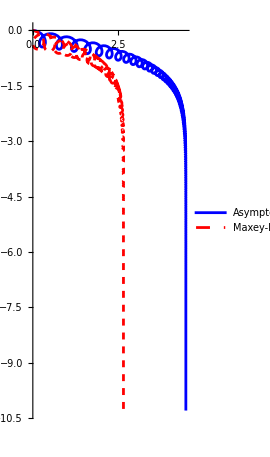

```mathematica
params = {eps->0.3,vS->0.01,b->0.9,St->0.1};
ux[x_,z_,t_]=Exp[z] Cos[x-t];
uz[x_,z_,t_]=Exp[z] Sin[x-t];

(*material derivative,with particle velocity (xd,zd)*)
Dux[x_,z_,t_,xd_,zd_]=D[ux[x,z,t],t]+xd D[ux[x,z,t],x]+zd D[ux[x,z,t],z];
Duz[x_,z_,t_,xd_,zd_]=D[uz[x,z,t],t]+xd D[uz[x,z,t],x]+zd D[uz[x,z,t],z];
sol=NDSolve[{x''[t]==(1/St) (eps ux[x[t],z[t],t]-x'[t])+b eps Dux[x[t],z[t],t,x'[t],z'[t]],z''[t]==(1/St) (eps uz[x[t],z[t],t]-z'[t]-vS)+b eps Duz[x[t],z[t],t,x'[t],z'[t]],x[0]==0,z[0]==0,x'[0]==0,z'[0]==0}/. params,{x,z},{t,0,1000}];
(z/.sol[[1]])[500]
zexpr/.{t->500}/.params

Show[ParametricPlot[Evaluate[{Xexpr+t,zexpr}/. params],{t,0,1000},PlotRange->All,PlotStyle->Blue,PlotLegends->{"Asymptotics"}],ParametricPlot[Evaluate[{x[t],z[t]}/. sol],{t,0,1000},PlotStyle->{Red,Dashed},PlotLegends->{"Maxey-Riley"}]]
```